```mathematica
a:=0.01
```

```mathematica
s:=0.02
```

```mathematica
f[z_]:=a*Exp[-z^2/s^2/2]/2
```

```mathematica
c:=1000
```

```mathematica
U[z_, t_]:=f[z+c*t]+f[z-c*t]
```

```mathematica
V[z_, t_]:=Expand[D[U[z, t],t]]
```

```mathematica
V[z, t]
```

-1.25×10^7 ⅇ^(-1250. (-1000 t+z)^2) t-1.25×10^7 ⅇ^(-1250. (1000 t+z)^2) t+12500. ⅇ^(-1250. (-1000 t+z)^2) z-12500. ⅇ^(-1250. (1000 t+z)^2) z

```mathematica
A[z_, t_]:=D[D[U[z, t],t],t]
```

```mathematica
A[z, t]
```

-1.25×10^7 ⅇ^(-1250. (-1000 t+z)^2)-1.25×10^7 ⅇ^(-1250. (1000 t+z)^2)+3.125×10^10 ⅇ^(-1250. (-1000 t+z)^2) (-1000 t+z)^2+3.125×10^10 ⅇ^(-1250. (1000 t+z)^2) (1000 t+z)^2

```mathematica
V[z,t]
```

-1.25×10^7 ⅇ^(-1250. (-1000 t+z)^2) t-1.25×10^7 ⅇ^(-1250. (1000 t+z)^2) t+12500. ⅇ^(-1250. (-1000 t+z)^2) z-12500. ⅇ^(-1250. (1000 t+z)^2) z

```mathematica
V[z,t] /. t->0
```

0.

```mathematica
A[z,t] /. t->0
```

-2.5×10^7 ⅇ^(-1250. z^2)+6.25×10^10 ⅇ^(-1250. z^2) z^2

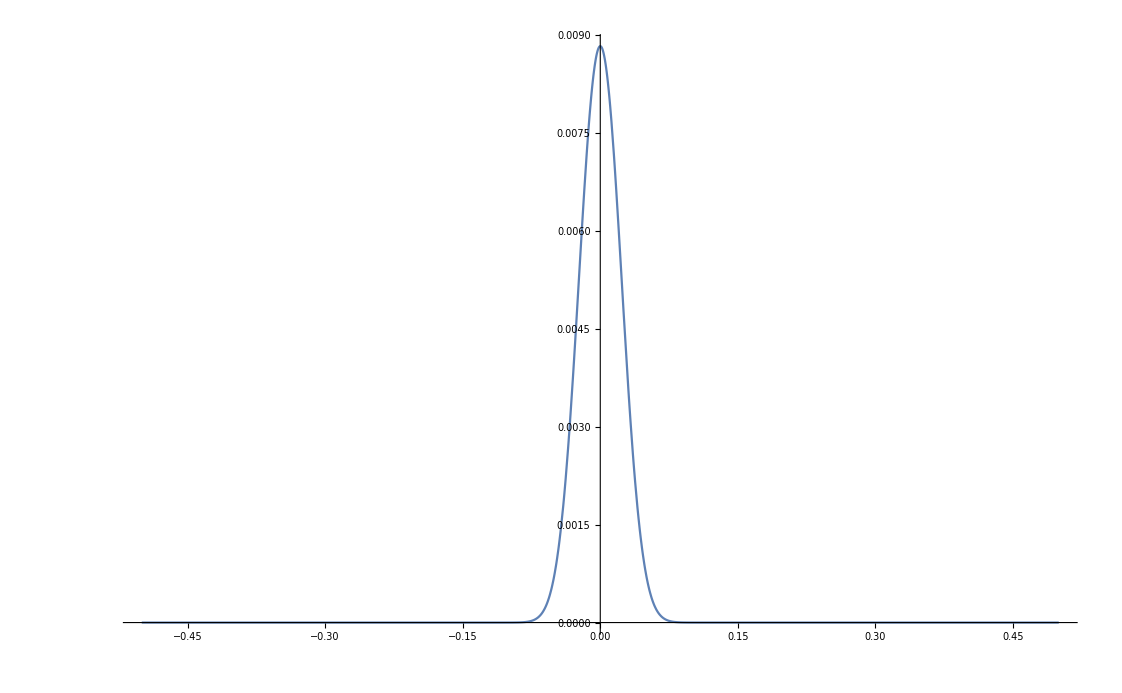

```mathematica
Plot[U[z,t]/.t->0.00001,{z,-1/2,1/2},PlotRange->All]
```

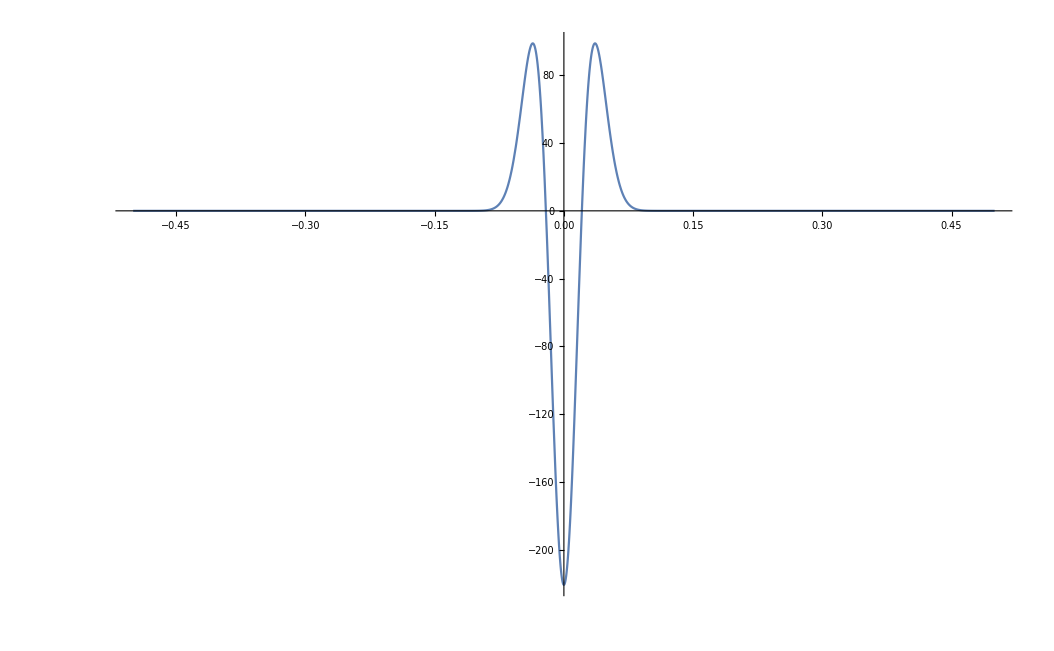

```mathematica
Plot[D[U[z, t],t]/.t->0.00001,{z,-1/2,1/2},PlotRange->All]
```

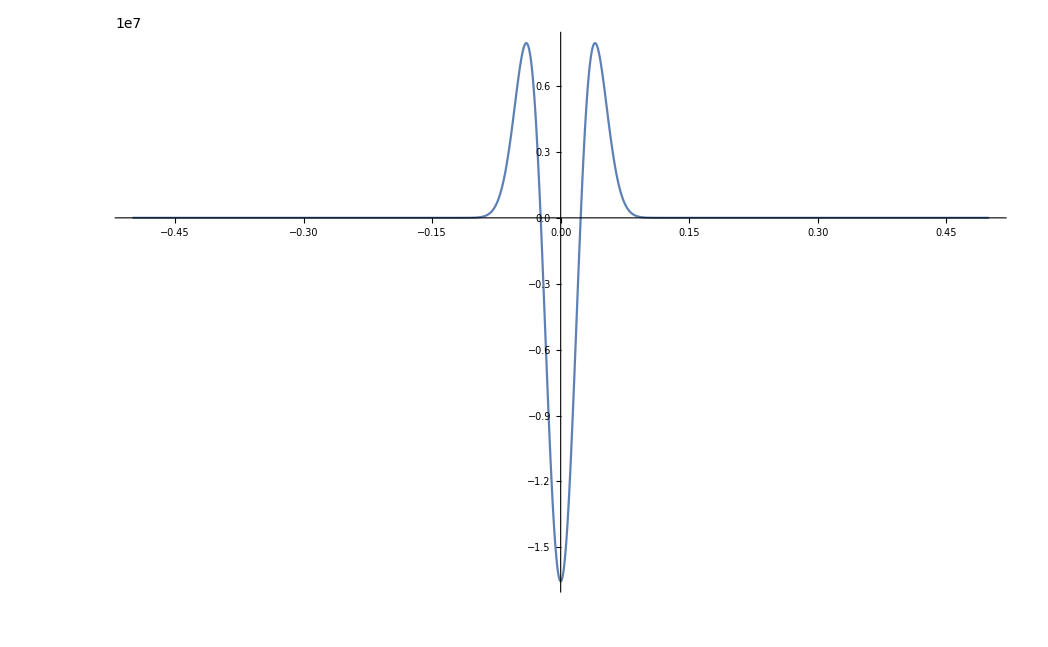

```mathematica
Plot[D[D[U[z, t],t],t]/.t->0.00001,{z,-1/2,1/2},PlotRange->All]
```

```mathematica
sig[z_,t_]:=-10^9*(f[z+c*t]*(z+c*t)/s/s+f[z-c*t]*(z-c*t)/s/s)
```

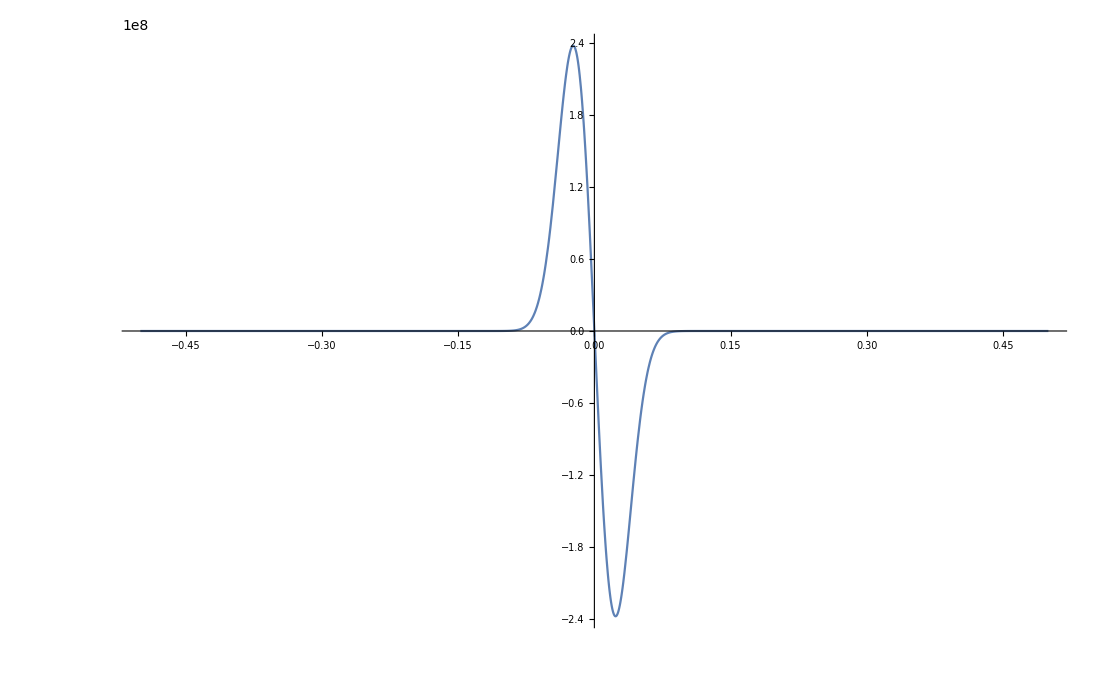

```mathematica
Plot[sig[z,t]/.t->0.00001,{z,-1/2,1/2},PlotRange->All]
```

```mathematica
FindMaximum[D[D[U[z, t],t],t]/.t->0.00001, {z,0.05}]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{7.95633×10^6,{z→0.0401058}}

```mathematica
D[U[z, t],t]/.z->0.036/.t->0.00001
```

98.7781